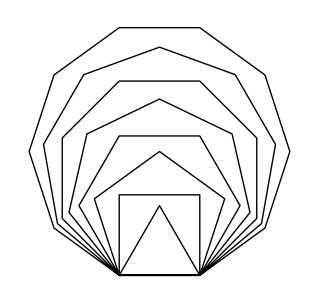

```mathematica
(*REPEAT 4[FOR 200 DRAW RT 90]画正方形*)
Graphics@Line@AnglePath[Flatten[Table[360°/#,{#}]&/@Range@10]]
```

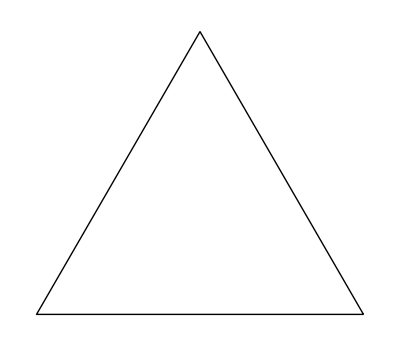
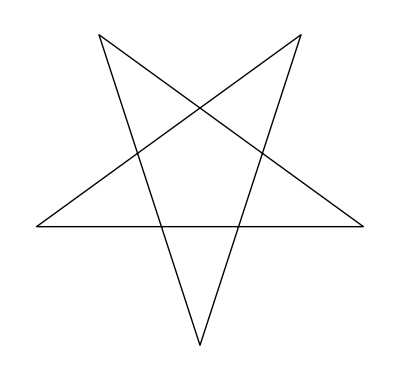
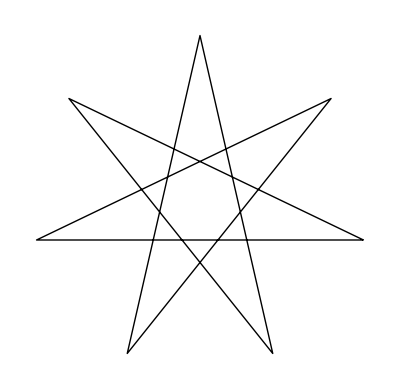
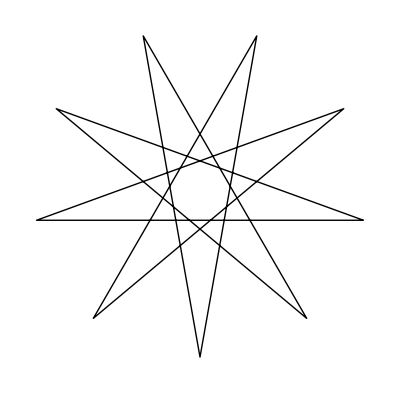
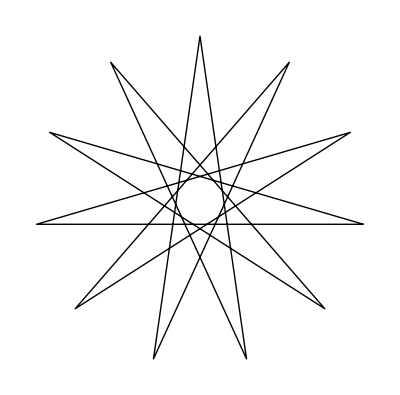

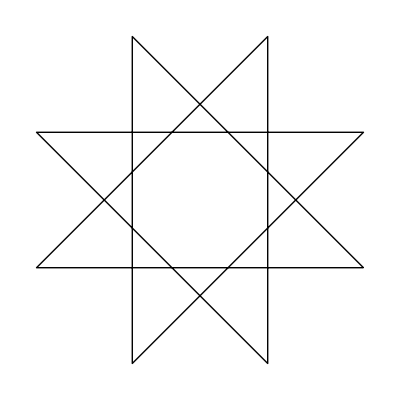
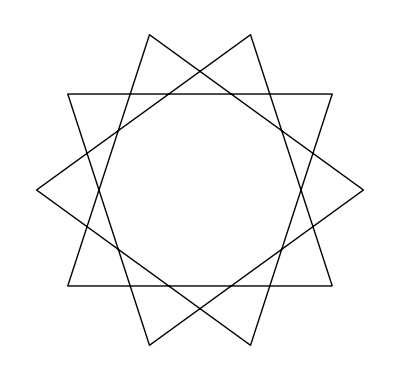
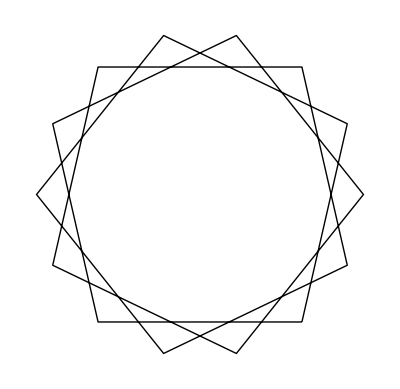

```mathematica
(*五角星大概是: REPEAT 5[FD 100 LT 180-180/5]*)
Graphics@Line@AnglePath[Table[180°-180°/#,{#}]]&/@Range[3,11,2]
Graphics@Line@AnglePath[Table[1080°/#,{#}]]&/@{8,10,14,16,20}
```

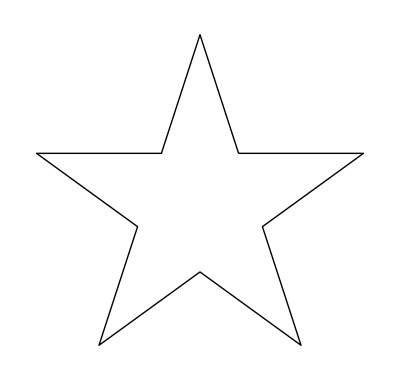

```mathematica
(*空心五角星 REPEAT 5[FD 20 RT 180-180/5 FD 20 LT 180-540/5]*)
Graphics@Line@AnglePath@Prepend[Riffle[Array[144 °&,5],-72 °],108 °]
```

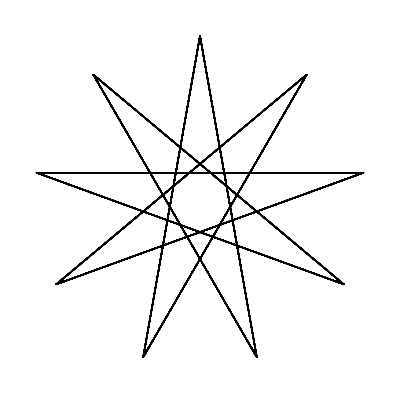
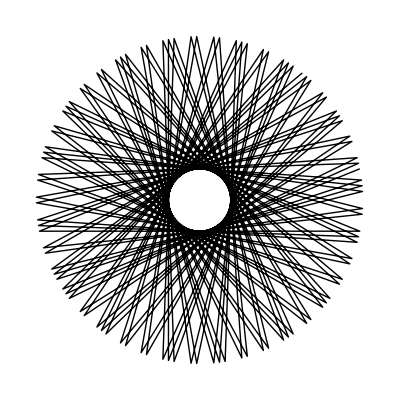
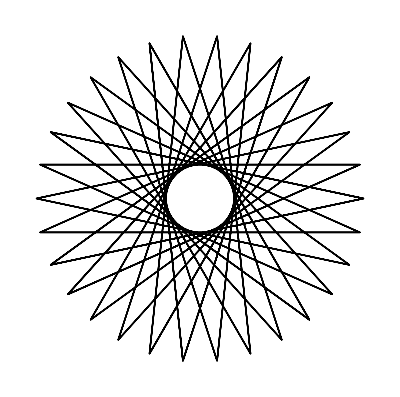
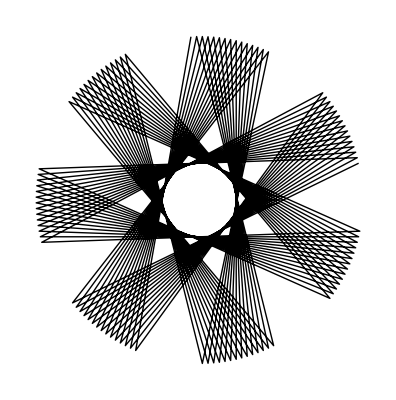
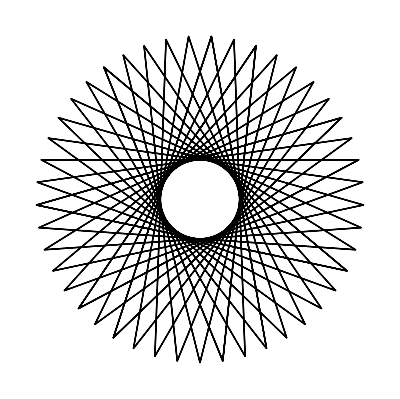
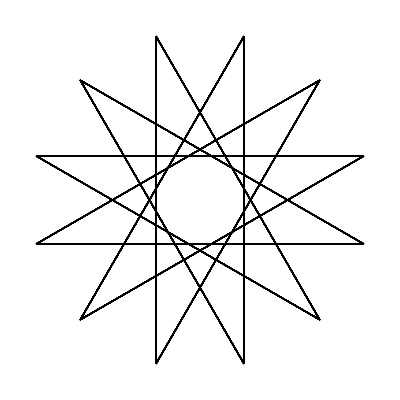
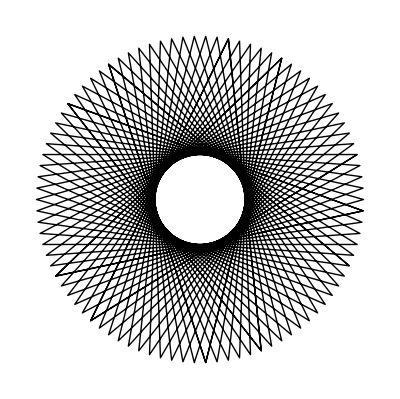
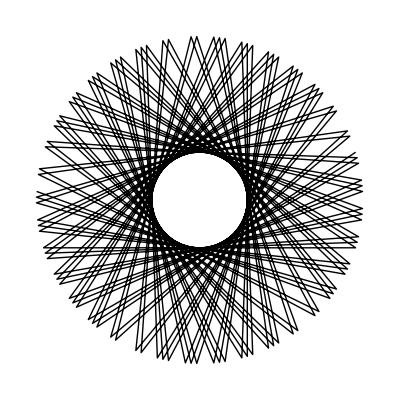

```mathematica
Table[Graphics@Line@AnglePath[ConstantArray[Pi n/90,100]],{n,100,120}]
```

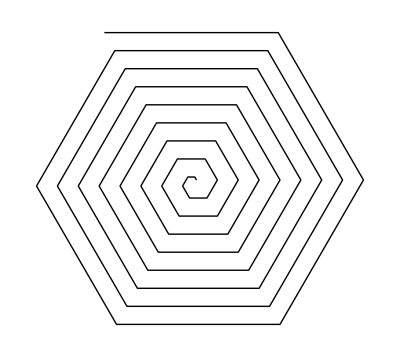
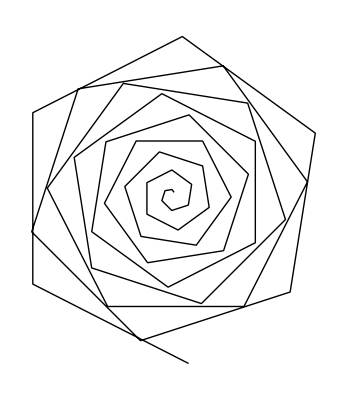
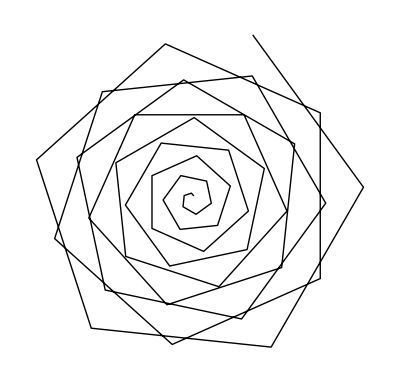
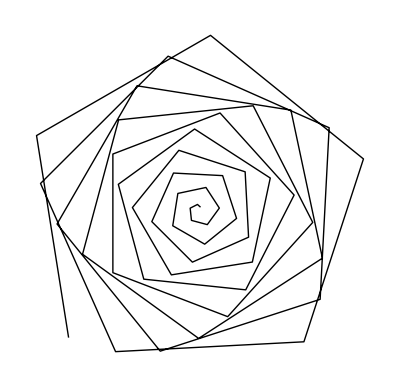
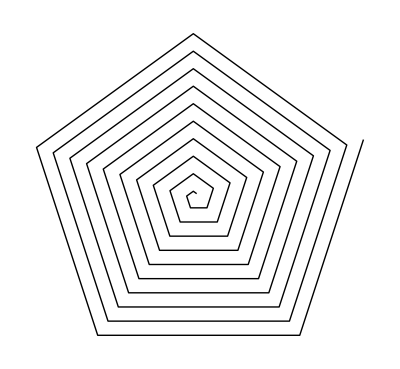
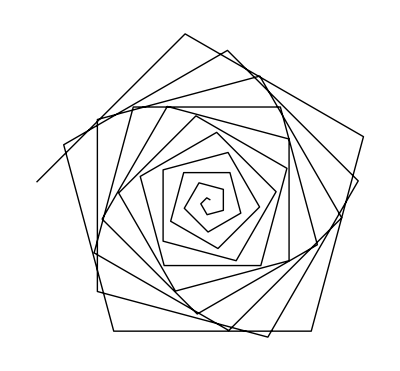
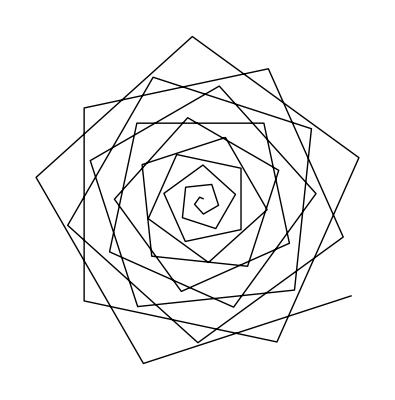
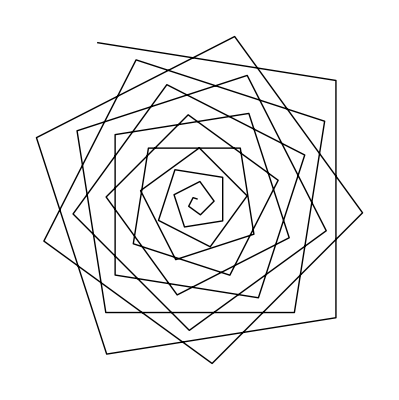

```mathematica
rot[θ_,dr_]:=Graphics@Line@AnglePath[Table[{r,θ},{r,0,1,dr}]]
Table[rot[Pi n/90,0.02],{n,30,60,1.5}]
```

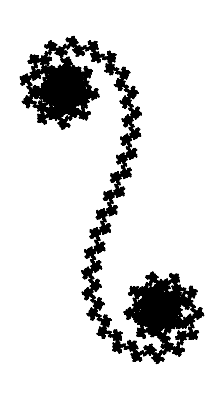

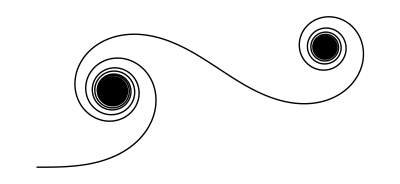

```mathematica
Rotate[Graphics@Line@AnglePath@N@Range[100000],Pi/2]
Graphics[Line[AnglePath[N@Range[0,10,0.001]]]]
```

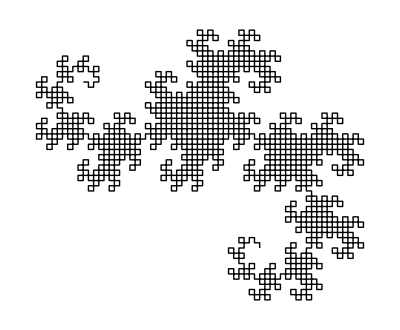

```mathematica
Graphics@Line@AnglePath[1/2 π KroneckerSymbol[-1,Range@2048]]
```

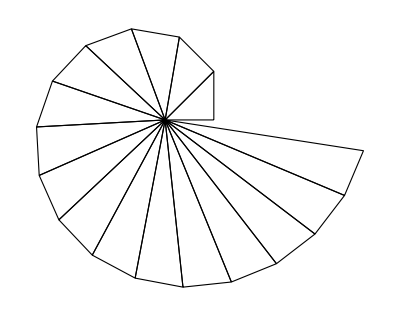

```mathematica
Graphics[{FaceForm[None],EdgeForm[Black],Polygon[PadRight[#,{3,2}]]&/@Partition[AnglePath[{{1,0},π/2},Prepend[ArcCot[Sqrt[Range[15]]],0]],2,1]}]
```

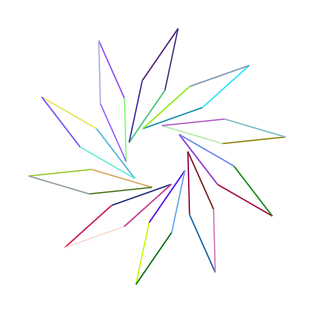

```mathematica
Table[Rotate[Line[AnglePath[{{-0.7,-0.7},(-Pi/6)},{{2,(7 π)/8},{2,π/8},{2,(7 π)/8},{2,π/8}}]],i*Pi/5,{0,0}],{i,10}]/.l_Line:>ReplaceList[l,Line[{___,pt1_,pt2_,___}]:>{RandomColor[],Line[{pt1,pt2}]}]//Graphics
```

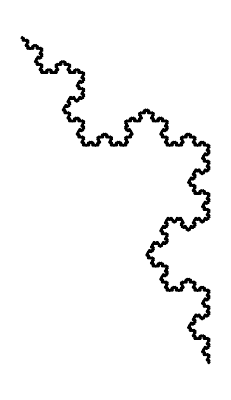

```mathematica
Rotate[Graphics@Line@AnglePath[Array[ThueMorse,4096]2 Pi/3],Pi/3]
```

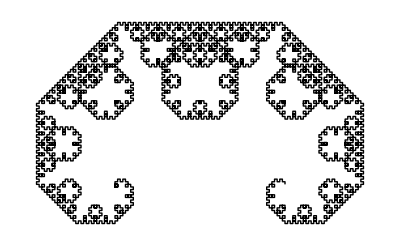

```mathematica
(Graphics[Line[AnglePath[(-1)^# Pi/2]]]&/@
SubstitutionSystem[{0->{0,0,1},1->{1}},{0},11])[[-1]]
```

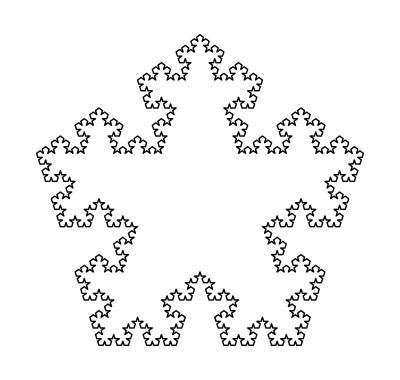

```mathematica
Graphics@Line[AnglePath[Nest[Flatten[{1,-2,1,#}&/@#]&
,{1,1,1,1,1},4] 2Pi/5]]
```

```mathematica
Curlicues:
```

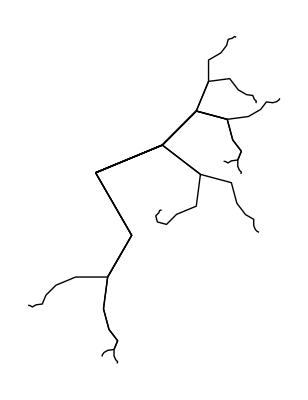

```mathematica
Graphics[Line[AnglePath/@Table[{0.666^i,RandomChoice[{-Pi/3,Pi/8}]},{10},{i,10}]]]
```

```mathematica
Rotate[Graphics[BSplineCurve[Map[AnglePath[Transpose[{0.666^Range[10],#}]]&,
Tuples[{-Pi/3,Pi/8},10]]]],Pi/2]
```

-Graphics-

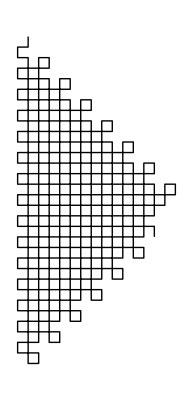

```mathematica
Rotate[Graphics[Line[AnglePath[Pi/2*Table[(-1)^((1+RudinShapiro[n]
RudinShapiro[n+1])/2),{n,0,500}]]]],Pi/2]
```

```mathematica
108*12
```

1296

```mathematica
135*8
```

1080

```mathematica
AnglePath
```